# Woods-Saxon Potential

Authors:
School Of Physical Sciences and Nanotechnology

```mathematica
V0=1;
L=2;
```

```mathematica
Vx[x_,a_]:= V0 (HeavisideTheta[-x]/(1+Exp[-a(x+L)])+HeavisideTheta[x]/(1+Exp[a (x-L)]));
```

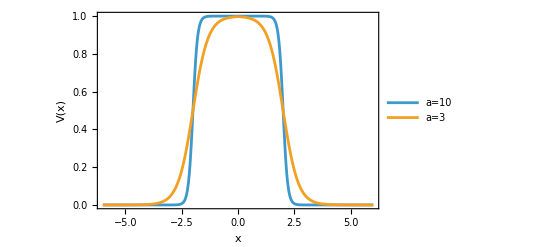

```mathematica
Plot[{Vx[x,10],Vx[x,3]},{x,-6,6},PlotRange->All,Frame->True,FrameLabel->{"x","V(x)"},PlotLegends->{"a=10","a=3"}]
```

## Scattering Solutions

### For x<0 with E^2>1 the Klein Gordon equation is:

```mathematica
Clear[V0,a,L];
```

```mathematica
eq1= Subscript[ϕ, L]''[x] + ((En-V0/(1+Exp[-a(x+L)]))^2-1) Subscript[ϕ, L][x]==0;
```

Let

```mathematica
y[x_]:=-Exp[-a(x+L)]
```

```mathematica
eq1/.{Subscript[ϕ, L]''[x]-> a^2 y^2 D[y  D[Subscript[ϕ, L][y],y],y]}
```

(-1+(En-V0/(1+ⅇ^(-a (L+x))))^2) ϕ_L[x]+a^2 y^2 (ϕ_L'[y]+y ϕ_L''[y])==0

```mathematica
eq2 = (-1+(En-V0/(1-y))^2) Subscript[ϕ, L][x]+a^2 y^2 (Subscript[ϕ, L]'[y]+y Subscript[ϕ, L]''[y])==0
```

(-1+(En-V0/(1-y))^2) ϕ_L[x]+a^2 y^2 (ϕ_L'[y]+y ϕ_L''[y])==0

Let

```mathematica
Subscript[ϕ, L][y_]:= y^μ(1-y)^(-Subscript[λ, 1])f[y];
```

```mathematica
eq3=D[y D[Subscript[ϕ, L][y],y],y ]//FullSimplify
```

(1-y)^(-2-λ_1) y^(-1+μ) (f[y] ((-1+y)^2 μ^2+y λ_1 (1+2 μ-2 y μ+y λ_1))+(-1+y) y (((-1+y) (1+2 μ)-2 y λ_1) f'[y]+(-1+y) y f''[y]))

Substituting equation 3 into equation 2 we get:

```mathematica
eq4= (-1+(En-V0/(1-y))^2) Subscript[ϕ, L][x]+a^2 y^2 ((1-y)^(-2-Subscript[λ, 1]) y^(-1+μ) (f[y] ((-1+y)^2 μ^2+y Subscript[λ, 1] (1+2 μ-2 y μ+y Subscript[λ, 1]))+(-1+y) y (((-1+y) (1+2 μ)-2 y Subscript[λ, 1]) f'[y]+(-1+y) y f''[y])))==0 //Simplify
```

(1-x)^-λ_1 x^μ (-1+(En+V0/(-1+y))^2) f[x]+a^2 (1-y)^(-2-λ_1) y^(1+μ) (f[y] ((-1+y)^2 μ^2+y λ_1 (1-2 (-1+y) μ+y λ_1))+(-1+y) y (((-1+y) (1+2 μ)-2 y λ_1) f'[y]+(-1+y) y f''[y]))==0

Expand the first term in equation 4

```mathematica
-1+((En(1-y)-V0)^2//ExpandAll)/(1-y)^2
```

-1+(En^2-2 En V0+V0^2-2 En^2 y+2 En V0 y+En^2 y^2)/(1-y)^2

Replace in equation 4 :

```mathematica
eq4= ((-(1-y)^2+En^2-2 En V0+V0^2-2 En^2 y+2 En V0 y+En^2 y^2)/(1-y)^2) Subscript[ϕ, L][x]+a^2 y^2 ((1-y)^(-2-Subscript[λ, 1]) y^(-1+μ) (f[y] ((-1+y)^2 μ^2+y Subscript[λ, 1] (1+2 μ-2 y μ+y Subscript[λ, 1]))+(-1+y) y (((-1+y) (1+2 μ)-2 y Subscript[λ, 1]) f'[y]+(-1+y) y f''[y])))==0 //Simplify
```

1/(-1+y)^2((1-x)^-λ_1 x^μ (V0^2+2 En V0 (-1+y)-(-1+y)^2+En^2 (-1+y)^2) f[x]+a^2 (1-y)^-λ_1 y^(1+μ) (f[y] ((-1+y)^2 μ^2+y λ_1 (1-2 (-1+y) μ+y λ_1))+(-1+y) y (((-1+y) (1+2 μ)-2 y λ_1) f'[y]+(-1+y) y f''[y])))==0

Then  solving the hypergeometric differential equation we get:

```mathematica
eq5 = y (1-y) f''[y] + ((1+2 μ)-(2 μ - 2 Subscript[λ, 1]+1) y )f'[y]-(μ-Subscript[λ, 1]+ν)(μ-Subscript[λ, 1]-ν) f[y]==0
```

-f[y] (μ-ν-λ_1) (μ+ν-λ_1)+(1+2 μ-y (1+2 μ-2 λ_1)) f'[y]+(1-y) y f''[y]==0

Where

```mathematica
μ[En_]:=(√(1-(En-V0)^2))/a;
k[En_]:=√(En^2-1);
ν[En_]:=(ⅈ k[En])/a;
λ[En_]:=(√(a^2-4 V0^2))/(2 a);
λ1[En_]:=-1/2+λ[En];
```

The solution of equation 5 can be expressed in terms of Gauss hypergeometric functions as:

```mathematica
f[y]= D1 Hypergeometric2F1[μ-ν-λ1,μ+ν-λ1,1+2μ,y]+D2 y^(-2μ)Hypergeometric2F1[-μ-ν-λ1,-μ+ν-λ1,1-2μ,y];
```

The we get

```mathematica
Subscript[ϕ, L][y]
```

(1-y)^-λ_1 y^μ (D2 y^(-2 μ) Hypergeometric2F1[-λ1-μ-ν,-λ1-μ+ν,1-2 μ,y]+D1 Hypergeometric2F1[-λ1+μ-ν,-λ1+μ+ν,1+2 μ,y])

Thus we define

```mathematica
ϕL[x_,En_]:=D1 y[x]^μ[En] (1-y[x])^(-λ1[En]) Hypergeometric2F1[μ[En]-ν[En]-λ1[En],μ[En]+ν[En]-λ1[En],1+2 μ[En],y[x]]+ D2 y[x]^(-μ[En])(1-y[x])^(-λ1[En]) Hypergeometric2F1[-μ[En]-ν[En]-λ1[En],-μ[En]+ν[En]-λ1[En],1-2 μ[En],y[x]]
```

### Asymptotic Behaviour (x<0)

Let' s check the asymptotic behaviour of the solution ϕ_L[y]

when x→∞

```mathematica
Asymptotic[y[x],x->-∞]
```

-ⅇ^(-a (L+x))

```mathematica
asy1 =Asymptotic[Subscript[ϕ, L][y],y->-∞]//Simplify
```

(1-y)^-λ_1 (-y)^(λ1-μ-ν) y^(-1-μ) ((D2 (-y)^(2 μ) (y+λ1^2-μ^2+2 y ν-2 λ1 ν+ν^2) Gamma[1-2 μ] Gamma[-2 ν])/((1+2 ν) Gamma[-λ1-μ-ν] Gamma[1+λ1-μ-ν])+(D1 y^(2 μ) (y+λ1^2-μ^2+2 y ν-2 λ1 ν+ν^2) Gamma[1+2 μ] Gamma[-2 ν])/((1+2 ν) Gamma[-λ1+μ-ν] Gamma[1+λ1+μ-ν])-(D2 (-y)^(2 (μ+ν)) (y+λ1^2-μ^2-2 y ν+2 λ1 ν+ν^2) Gamma[1-2 μ] Gamma[2 ν])/((-1+2 ν) Gamma[-λ1-μ+ν] Gamma[1+λ1-μ+ν])-(D1 (-y)^(2 ν) y^(2 μ) (y+λ1^2-μ^2-2 y ν+2 λ1 ν+ν^2) Gamma[1+2 μ] Gamma[2 ν])/((-1+2 ν) Gamma[-λ1+μ+ν] Gamma[1+λ1+μ+ν]))

We identify the coefficients A and B in terms of D1 and D2:

```mathematica
A[En_]:=D1 ((Gamma[1-2 μ[En]] Gamma[-2 ν[En]] (-1)^(-μ[En]))/(Gamma[-μ[En] - ν[En] -λ1[En]]Gamma[1-μ[En]-ν[En]+λ1[En]]))+D2 ((Gamma[1+2 μ[En]] Gamma[-2 ν[En]](-1)^μ[En])/(Gamma[μ[En]-ν[En]-λ1[En]] Gamma[1+μ[En]-ν[En]+λ1[En]]));
B[En_] :=D1 ((Gamma[1-2 μ[En]] Gamma[2 ν[En]] (-1)^(-μ[En]))/(Gamma[-μ[En] + ν[En] -λ1[En]]Gamma[1-μ[En]+ν[En]+λ1[En]]))+D2 ((Gamma[1+2 μ[En]] Gamma[2 ν[En]](-1)^μ[En])/(Gamma[μ[En]+ν[En]-λ1[En]] Gamma[1+μ[En]+ν[En]+λ1[En]]));
```

There fore  the asymptotic behavior of ϕ_L[X] can be written as:

```mathematica
Subscript[ϕ, 2L][x_]:=A Exp[ⅈ k(x+L)]+B Exp[-ⅈ k (x+L)]
```

### For x>0 with the Klein Gordon equation is:

```mathematica
Clear[V0,a,L];
```

```mathematica
eqR1= Subscript[ϕ, R]''[x] + ((En-V0/(1+Exp[a(x-L)]))^2-1) Subscript[ϕ, R][x]==0;
```

Let

```mathematica
z[x_]:=1/(1+Exp[a(x-L)])
```

```mathematica
z'[x]
```

-(a ⅇ^(a (-L+x)))/((1+ⅇ^(a (-L+x)))^2)

Thus, dϕR[x]/dz is:

```mathematica
Subscript[ϕ, R]'[z] z'[x]
```

-(a ⅇ^(a (-L+x)) ϕ_R'[z])/((1+ⅇ^(a (-L+x)))^2)

and (d^2 ϕR[x])/dz^2 is:

```mathematica
-(a ⅇ^(a (L+x)) Subscript[ϕ, R]'[z])/((1+ⅇ^(a (L+x)))^2) D[-(a ⅇ^(a (L+x)) Subscript[ϕ, R]'[z])/((1+ⅇ^(a (L+x)))^2),z]
```

(a^2 ⅇ^(2 a (L+x)) ϕ_R'[z] ϕ_R''[z])/((1+ⅇ^(a (L+x)))^4)

Therefore

```mathematica
eqR1/.{1/(1+Exp[a(x-L)])->z, Subscript[ϕ, R]''[x] -> (a^2 ⅇ^(2 a (L+x)) Subscript[ϕ, R]'[z] Subscript[ϕ, R]''[z])/((1+ⅇ^(a (L+x)))^4)}
```

(-1+(En-V0 z)^2) ϕ_R[x]+(a^2 ⅇ^(2 a (L+x)) ϕ_R'[z] ϕ_R''[z])/((1+ⅇ^(a (L+x)))^4)==0

Let

```mathematica
Subscript[ϕ, R][z_]:= z^-ν(1-z)^-μ g[z];
```

```mathematica
eqR3=a^2 z(1-z) D[z (1-z)  D[Subscript[ϕ, R][z],z],z ]//FullSimplify
```

a^2 (1-z)^-μ z^-ν ((ν^2+z^2 (-1+μ+ν) (μ+ν)-z (μ+ν) (-1+2 ν)) g[z]+(-1+z) z ((-1+2 ν-2 z (-1+μ+ν)) g'[z]+(-1+z) z g''[z]))

Substituting equation 3 into equation 2 we get:

```mathematica
eqR4= (-1+(En-V0 z)^2) Subscript[ϕ, R][x]+a^2 (1-z)^-μ z^-ν ((ν^2+z^2 (-1+μ+ν) (μ+ν)-z (μ+ν) (-1+2 ν)) g[z]+(-1+z) z ((-1+2 ν-2 z (-1+μ+ν)) g'[z]+(-1+z) z g''[z]))==0 //Simplify
```

(1-x)^-μ x^-ν (-1+(En-V0 z)^2) g[x]+a^2 (1-z)^-μ z^-ν ((ν^2+z^2 (-1+μ+ν) (μ+ν)-z (μ+ν) (-1+2 ν)) g[z]+(-1+z) z ((-1+2 ν-2 z (-1+μ+ν)) g'[z]+(-1+z) z g''[z]))==0

Expand the first term in equation 4

```mathematica
(1-x)^-μ x^-ν (-1+(En-V0 z)^2) g[x]//Expand
```

-(1-x)^-μ x^-ν g[x]+En^2 (1-x)^-μ x^-ν g[x]-2 En V0 (1-x)^-μ x^-ν z g[x]+V0^2 (1-x)^-μ x^-ν z^2 g[x]

Replace in equation 4 :

```mathematica
eqR4= -(1-x)^-μ x^-ν g[x]+En^2 (1-x)^-μ x^-ν g[x]-2 En V0 (1-x)^-μ x^-ν z g[x]+V0^2 (1-x)^-μ x^-ν z^2 g[x]+a^2 (1-z)^-μ z^-ν ((ν^2+z^2 (-1+μ+ν) (μ+ν)-z (μ+ν) (-1+2 ν)) g[z]+(-1+z) z ((-1+2 ν-2 z (-1+μ+ν)) g'[z]+(-1+z) z g''[z]))==0//Simplify
```

(1-x)^-μ x^-ν (-1+En^2-2 En V0 z+V0^2 z^2) g[x]+a^2 (1-z)^-μ z^-ν ((ν^2-z (μ+ν) (-1+2 ν)+z^2 (μ^2+(-1+ν) ν+μ (-1+2 ν))) g[z]-(-1+z) z ((1-2 ν+2 z (-1+μ+ν)) g'[z]-(-1+z) z g''[z]))==0

Then  solving the hypergeometric differential equation we get:

```mathematica
eqR5 = z(1-z) g''[z] +g'[z]   [(1-2 ν)-2(1-ν-μ) z]-(1/3-ν-μ+λ) g[z]==0
```

-((1/3+λ-μ-ν) g[z])+(1-z) z g''[z]+g'[z][1-2 z (1-μ-ν)-2 ν]==0

Where

The solution of equation R5 can be expressed in terms of Gauss hypergeometric functions as:

```mathematica
g[z]= d1  Hypergeometric2F1[1/2-ν-μ-λ,1/2-ν-μ+λ,1-2ν,z]+d2 z^(2ν) Hypergeometric2F1[1/2+ν-μ-λ,1/2+ν-μ+λ,1+2ν,z];
```

The we get

```mathematica
Subscript[ϕ, R][z]/.d2->0
```

d1 (1-z)^-μ z^-ν Hypergeometric2F1[1/2-λ-μ-ν,1/2+λ-μ-ν,1-2 ν,z]

We keep only the solution for the transmitted wave, i.e., d2=2.

```mathematica
ϕR[x_,En_]:=d1 z[x]^(-ν[En])(1-z[x])^(-μ[En]) Hypergeometric2F1[1/2-ν[En]-μ[En]-λ[En],1/2-ν[En]-μ[En]+λ[En],1-2 ν[En],z[x]]
```

### Asymptotic Behaviour (x<0)

Let' s check the asymptotic behaviour of the solution ϕ_L[y]. We have that

```mathematica
Limit[z[x],x->∞]
```

ConditionalExpression[0, L∈ℝ&&a>0]

We see that z →0, Then

```mathematica
Hypergeometric2F1[1/2-ν[En]-μ[En]-λ[En],1/2-ν[En]-μ[En]+λ[En],1-2 ν[En],z[x]]/.z[x]->0
```

1

And

```mathematica
(1-z[x])^(-μ[En])/.z[x]->0
```

1

Thus,

```mathematica
asym =Asymptotic[d1 z[x]^(-ν[En])/.z[x]->Exp[a(x-L)],x->∞]/.ν->(ⅈ k)/a
```

d1 (ⅇ^(a (-L+x)))^(-(ⅈ √(-1+En^2))/a)

Where ν=(ⅈ k)/a.Therefore  ϕ_R[x] can be written as:

```mathematica
Subscript[ϕ, 2R][x_]:=d1 Exp[ⅈ k(x-L)]
```

## Matching Conditions

```mathematica
y0=y[0];z0=z[0];
dy0=D[y[x],x]/. x->0; 
dz0=D[z[x],x]/. x->0;
```

```mathematica
meq1[En_]:=(ϕL[0,En]==ϕR[0,En])/. {y[0]->y0,z[0]->z0};
meq2[En_]:=((D[ϕL[x,En],x]/. x->0)==(D[ϕR[x,En],x]/. x->0))/. {y[0]->y0,z[0]->z0,D[y[x],x]->dy0,D[z[x],x]->dz0};
```

We solve the system of equations to get D1 and D2

```mathematica
sol12[En_,wp_:80]:=Solve[SetPrecision[{meq1[En],meq2[En]},wp],{D1,D2},WorkingPrecision->wp][[1]];
```

Then we substitute the values of D1 and D2 into A and B parameters.

```mathematica
alphaBetaNum[aVal_,LVal_,V0Val_][En_?NumericQ]:=Module[{a=aVal,L=LVal,V0=V0Val,kE,s,x1,x2,g1,g2,M,rhs,Aover,Bover},kE=Sqrt[En^2-1];
s=sol12[En,80];(*D1,D2 in terms of d1*)(*choose two far-left points;-8/a and-10/a beyond-L work well*)x1=-L-8./a;x2=-L-10./a;
g1=(ϕL[x1,En]/. s)/d1;(* =(A e^{ik(x1+L)}+B e^{-ik(x1+L)})/d1*)
g2=(ϕL[x2,En]/. s)/d1;
M={{Exp[I kE (x1+L)],Exp[-I kE (x1+L)]},{Exp[I kE (x2+L)],Exp[-I kE (x2+L)]}};
rhs={g1,g2};
{Aover,Bover}=LinearSolve[N[M,80],N[rhs,80]];
{Aover,Bover} (* ={alpha,beta}*)];
```

#### Reflected Coefficient

```mathematica
Rnum[a_,L_,V0_][En_?NumericQ]:=Module[{α,β},{α,β}=alphaBetaNum[a,L,V0][En];
N[Abs[β/α]^2]];
```

#### Transmission Coefficient

```mathematica
Tnum[a_,L_,V0_][En_?NumericQ]:=Module[{α,β},{α,β}=alphaBetaNum[a,L,V0][En];
N[1/Abs[α]^2]];
```

### Plot 1

```mathematica
unitarityCheck[aVal_,LVal_,V0Val_,En_]:=Module[{},{a,L,V0}=N@{aVal,LVal,V0Val};
With[{T=Tnum[a,L,V0][En],R=Rnum[a,L,V0][En]},{T,R,T+R}//N]];
```

```mathematica
unitarityCheck[2,2,4,2.5]
```

{0.341365,0.658371,0.999737}

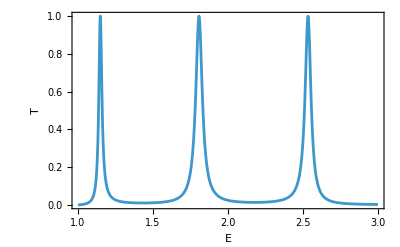

```mathematica
Plot[Tnum[2,2,4][En],{En,1,4-1},PlotRange->All,Frame->True,FrameLabel->{"E","T"}]
```

#### Test R+T=1

```mathematica
test1=Tnum[2,2,4][2.5]
```

0.341365

```mathematica
test2 =Rnum[2,2,4][2.5]
```

0.658371

```mathematica
test1+test2
```

0.999737

### Plot 2

```mathematica
unitarityCheck[2,2,3.1,2]
```

{0.00241187,0.997587,0.999999}

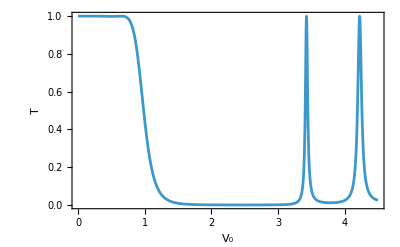

```mathematica
Plot[Tnum[2,2,V0][2],{V0,0,4.5},PlotRange->All,Frame->True,FrameLabel->{"V_0","T"}]
```

#### Test R+T=1

```mathematica
test1=Tnum[2,2,3.1][2]
```

0.0244948

```mathematica
test2 =Rnum[2,2,3.1][2]
```

0.975494

```mathematica
test1+test2
```

0.999989

### Plot 3

```mathematica
unitarityCheck[10,2,4,2.5]
```

{0.387278,0.612715,0.999993}

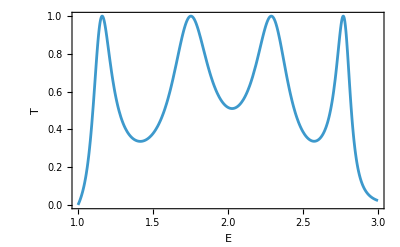

```mathematica
Plot[Tnum[10,2,4][En],{En,1,4-1},PlotRange->All,Frame->True,FrameLabel->{"E","T"}]
```

#### Test R+T=1

```mathematica
test1=Tnum[10,2,4][2.5]
```

0.387278

```mathematica
test2 =Rnum[10,2,4][2.5]
```

0.612715

```mathematica
test1+test2
```

0.999993

### Plot 4

```mathematica
unitarityCheck[10,2,3.1,2.5]
```

{0.0016793,0.998321,1.}

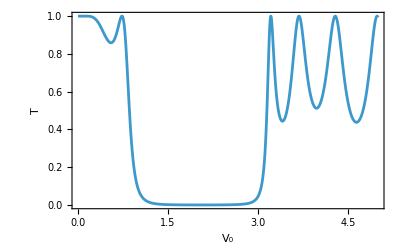

```mathematica
Plot[Tnum[10,2,V0][2],{V0,0,5},PlotRange->All,Frame->True,FrameLabel->{"V_0","T"}]
```

#### Test R+T=1

```mathematica
test1=Tnum[10,2,3.1][2.5]
```

0.0016793

```mathematica
test2 =Rnum[10,2,3.1][2.5]
```

0.998321

```mathematica
test1+test2
```

1.